## Masterfile for plots

This notebook explains how Fig. 3 of the dynamical systems review [arXiv:1712.03107] has been produced

#### Equations

```mathematica
Eqx=3 x[η] (-1+Subscript[w, m] (-1+x[η])+x[η]+y[η]+Subscript[w, r] y[η])
```

3 x[η] (-1+x[η]+(4 y[η])/3)

```mathematica
Eqy=3 y[η] (-1+x[η]+Subscript[w, m] x[η]+Subscript[w, r] (-1+y[η])+y[η])
```

3 y[η] (-1+x[η]+1/3 (-1+y[η])+y[η])

```mathematica
Subscript[w, m]=0;
Subscript[w, r]=1/3;
```

```mathematica
weff=-1+x+y+x Subscript[w, m]+y Subscript[w, r]/.x->x[η]/.y->y[η]
```

-1+x[η]+(4 y[η])/3

#### Numerical solutions

```mathematica
maxstep=10^4;
```

```mathematica
nsol1=NDSolve[{{Eqx,Eqy}=={x'[η],y'[η]}, x[0] ==.3,y[0]==1. 10^-6}, {x[η],y[η]}, {η, -100, 100},Method->StiffnessSwitching, AccuracyGoal->30,PrecisionGoal->15, MaxSteps->maxstep,StartingStepSize->0.001,MaxStepFraction->1/1000]
```

{{x[η]→InterpolatingFunction[{{-100.,100.}},<>][η],y[η]→InterpolatingFunction[{{-100.,100.}},<>][η]}}

#### Plotting

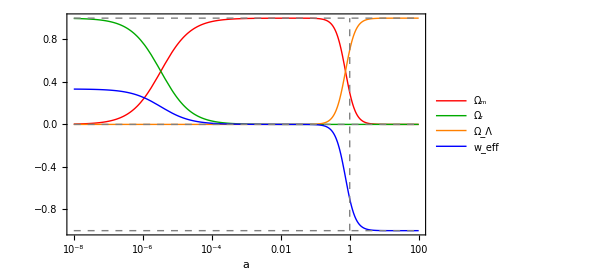

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->10,FrameMargins->0,Background->White]
figure=LogLinearPlot[Evaluate[{x[η],y[η],1-x[η]-y[η],weff,1,0,-1}/.nsol1[[1]]/.η->Log[a]],{a,10^-8,10^2},PlotStyle->{{Thick,Red},{Thick,Darker[Green]},{Thick,Orange},{Thick,Blue},{Dashed,Gray},{Dashed,Gray},{Dashed,Gray}},Ticks->{{None},{-1,-0.5,0,0.5,1}},TicksStyle->{15,15},Frame->{{True,False},{True,False}},FrameStyle->15,FrameLabel->{"a",None},Axes->None,PlotLegends->Placed[LineLegend[{"Ω_m","Ω_r","Ω_Λ","w_eff"},LegendFunction->frame],{1/4,1/4}],ImageSize->450,Epilog->{{Dashed,Gray,Line[{{0,-1},{0,1}}]}}]
```

#### Saving file

```mathematica
SetDirectory[NotebookDirectory[]];
Export["filename.pdf",figure]
```

filename.pdf